```mathematica
ClearAll["Global`*"]
```

```mathematica
(*solve with mathematica*)
```

```mathematica
sol=NDSolve[{u''''[x]-Cos[u[x]]==0,u[0]==0,u[1]==0,u'[0]==0,u'[1]==0},u,{x,0,1}][[1]]
```

{u→InterpolatingFunction[…]}

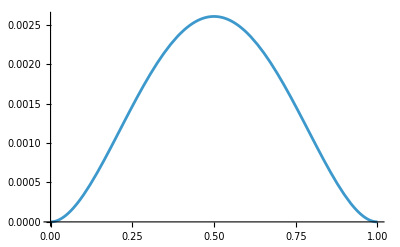

```mathematica
plotmathematica=Plot[u[x]/.sol,{x,0,1}]
```

```mathematica
(*import the solution with python*)
```

```mathematica
tab=Import["/Users/michelecastellana/Documents/finite_elements/solve_ode_with_python/fourth_order/solution.csv"]
tab=Drop[tab,{1}]
```

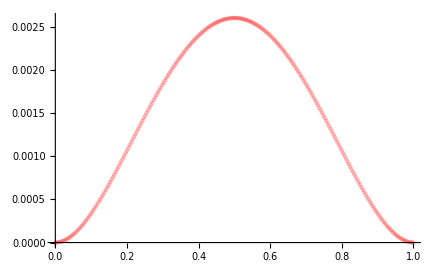

```mathematica
plotpython=ListPlot[tab,PlotStyle->{Red, Opacity->0.25}]
```

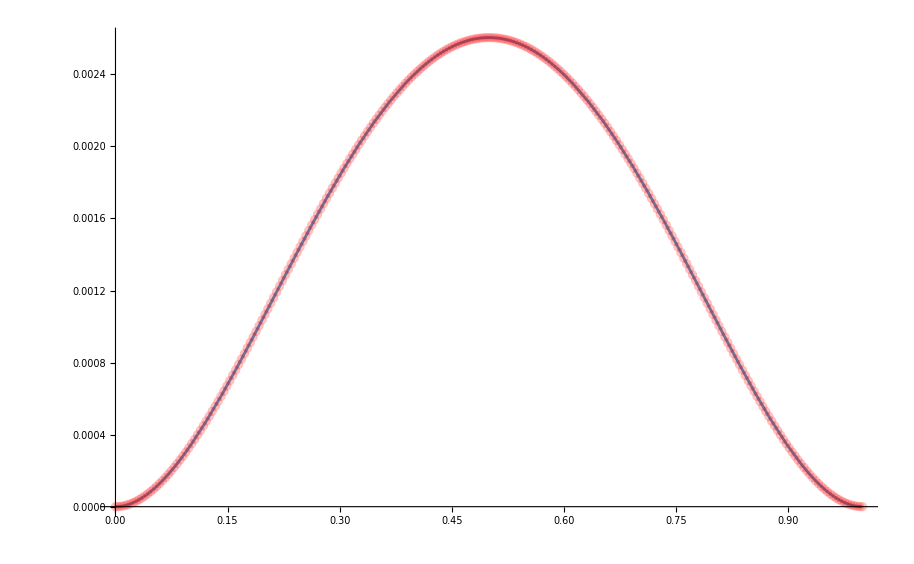

```mathematica
Show[plotmathematica,plotpython]
```